### Compute half-mass

```mathematica
mhalf=FullSimplify[Assuming[{τ,Y} ∈Reals && τ >1&&Y>0,Integrate[x/(1+x)^2(τ^2/(τ^2+x^2)),{x,0,Y}]]]
```

(τ^2 (-2 Y (1+τ^2)+4 (1+Y) τ ArcTan[Y/τ]+2 (1+Y) (-1+τ^2) Log[(1+Y) τ]-(1+Y) (-1+τ^2) Log[Y^2+τ^2]))/(2 (1+Y) (1+τ^2)^2)

### Compute total mass

```mathematica
mtot = FullSimplify[Assuming[{τ,Y} ∈Reals && τ >1&&Y>0,Integrate[x/(1+x)^2(τ^2/(τ^2+x^2)),{x,0,Infinity}]]]
```

(τ^2 (-1+(π-τ) τ+(-1+τ^2) Log[τ]))/((1+τ^2)^2)

### Plot the 2 cases for an examples

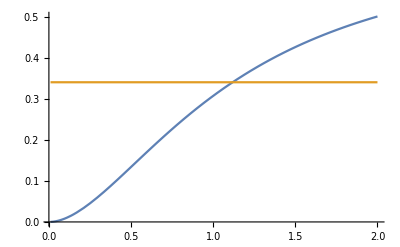

```mathematica
Plot[{2*mhalf/.τ->1.2,mtot/.τ->1.2},{Y,.01,2},PlotRange->Full]
```

### Ok they intersect, find solution numerically

```mathematica
tauSol[Y_]:=FindRoot[1/(1+Y)(-2 Y (1+τ^2)+4 (1+Y) τ ArcTan[Y/τ]+2 (1+Y) (-1+τ^2) Log[(1+Y) τ]-(1+Y) (-1+τ^2) Log[Y^2+τ^2])==(-1+(π-τ) τ+(-1+τ^2) Log[τ]),{τ,Y^1.7}]
```

### Make a table of solutions

```mathematica
τTab = Table[{Y,tauSol[Y][[1,2]]},{Y,0.01,2,0.01}];
```

### Plot it

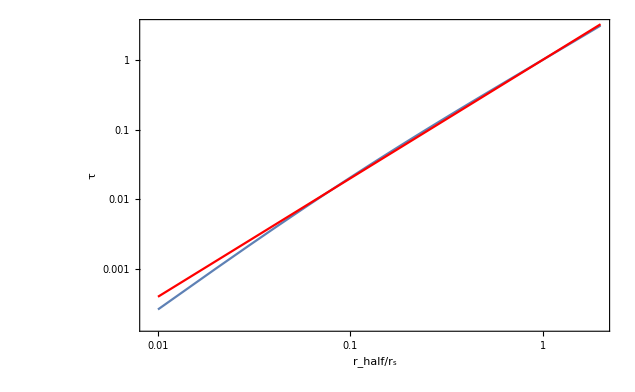

```mathematica
Show[ListLogLogPlot[τTab,Joined-> True,Frame->True,FrameLabel-> {Subscript[r, half]/Subscript[r, s],τ},LabelStyle->Directive[Bold, Medium,25],PlotRange->Full],LogLogPlot[x^1.7,{x,0.01,2},PlotStyle->Red]]
```

### Save to file

```mathematica
Export["tau_vs_xhalf.dat",τTab,"Data"]
```

tau_vs_xhalf.dat

### For fun, let’s try to derive the 2.1626 for NFW

```mathematica
FullSimplify[Assuming[{τ,X} ∈Reals && τ >1&&X>0,Difvmax = D[1/X 1/(2 (1+X) (1+τ^2)^2)τ^2 (-2 X (1+τ^2)+4 (1+X) τ ArcTan[X/τ]+2 (1+X) (-1+τ^2) Log[(1+X) τ]-(1+X) (-1+τ^2) Log[X^2+τ^2]),X]]]
```

(τ^2 (2 X (1+τ^2) (X+X^2+X^3+τ^2+2 X τ^2)-(1+X)^2 (X^2+τ^2) (4 τ ArcTan[X/τ]+(-1+τ^2) (2 Log[(1+X) τ]-Log[X^2+τ^2]))))/(2 X^2 (1+X)^2 (1+τ^2)^2 (X^2+τ^2))

```mathematica
Series[Difvmax,{τ,Infinity,2}]
```

(X+2 X^2-Log[1+X]-2 X Log[1+X]-X^2 Log[1+X])/(X^2 (1+X)^2)+(-6 X-9 X^2-2 X^3-X^4+6 Log[1+X]+12 X Log[1+X]+6 X^2 Log[1+X])/(2 X^2 (1+X)^2 τ^2)+O[1/τ]^3

Solve for the leading term in the derivative is zero (corresponding to v_max)

```mathematica
FindRoot[(X+2 X^2-Log[1+X]-2 X Log[1+X]-X^2 Log[1+X])/(X^2 (1+X)^2)==0,{X,2}]
```

{X→2.16258}

Victory!

### Study effect of τ

```mathematica
Tabtau[τh_]:= FindRoot[Difvmax/.τ-> τh,{X,0.005}]
```

### Make a table of solutions

```mathematica
XmaxTab = Table[{τ,Tabtau[τ][[1,2]]},{τ,.001,2,0.001}];
```

### Plot it

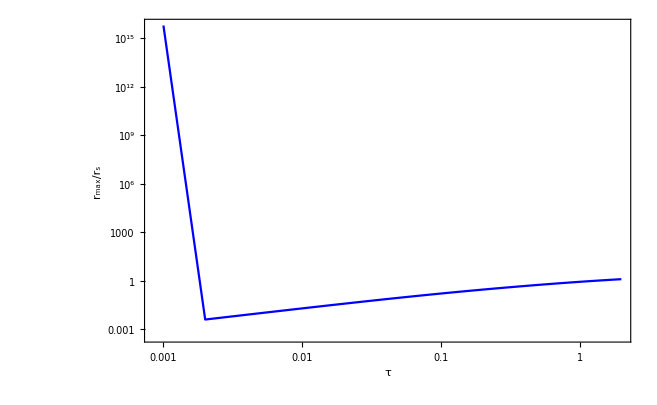

```mathematica
ListLogLogPlot[{XmaxTab},Joined-> True,Frame->True,PlotRange->Full,FrameLabel-> {τ,Subscript[r, max]/Subscript[r, s]},LabelStyle->Directive[Bold, Medium,25],PlotStyle->{Blue,Red}]
```

```mathematica
tautab = Table[{XmaxTab[[i,2]],XmaxTab[[i,1]]},{i,2,Length[XmaxTab]}];
```

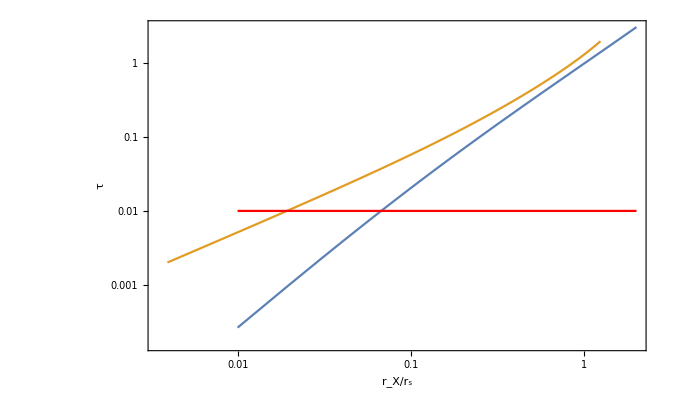

```mathematica
Show[ListLogLogPlot[{τTab,tautab },Joined-> True,Frame->True,FrameLabel-> {Subscript[r, X]/Subscript[r, s],τ},LabelStyle->Directive[Bold, Medium,25],PlotRange->Full],LogLogPlot[0.01,{x,0.01,2},PlotStyle->Red]]
```

```mathematica
1/0.8503555895558775
```

1.17598

### Save to file

```mathematica
Export["xmax_vs_tau.dat",XmaxTab,"Data"]
```

xmax_vs_tau.dat

## Try solving both at the same time

```mathematica
Sol[rh_,rmax_,τs_,rss_]:=FindRoot[{(1/(1+Y) (-2 Y (1+τ^2)+4 (1+Y) τ ArcTan[Y/τ]+2 (1+Y) (-1+τ^2) Log[(1+Y) τ]-(1+Y) (-1+τ^2) Log[Y^2+τ^2])/. Y-> rh/rs)/(-1+(π-τ) τ+(-1+τ^2) Log[τ])==1,(((τ^2 (2 X (1+τ^2) (X+X^2+X^3+τ^2+2 X τ^2)-(1+X)^2 (X^2+τ^2) (4 τ ArcTan[X/τ]+(-1+τ^2) (2 Log[(1+X) τ]-Log[X^2+τ^2]))))/(2 X^2 (1+X)^2 (1+τ^2)^2 (X^2+τ^2)))/.X-> rmax/rs)==0},{{τ,τs,0,2},{rs,rss,rmax/2.16258,15*rmax}}, MaxIterations->1000,AccuracyGoal->8]
```

1.14745

0.14934

{τ→0.908999,rs→0.169137}

{τ→0.88419}

0.799352

0.492566

0.000584363

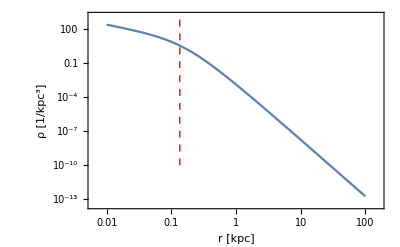

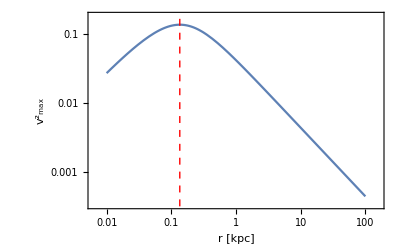

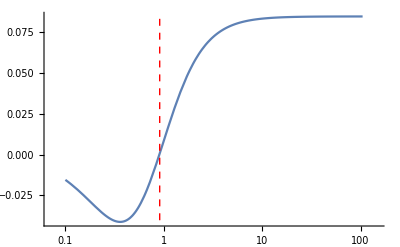

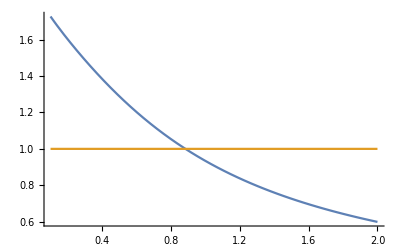

```mathematica
rmax =.1352;
α=1.16;
rh=α*rmax;
0.35 α^8
rmax/(0.5 α^4)
Solh=Sol[rh,rmax,0.35 α^8,rmax/(0.5 α^4)]
Solτ=tauSol[rh/rs]/.Solh[[2]]
Xsol=rmax/rs/.Solh[[2]]
lineStyle={Thick,Red,Dashed};
line1=Line[{{Log[rmax],Log[10^-10]},{Log[rmax],Log[3000]}}];
line2=Line[{{Log[Solh[[1,2]]],-0.3},{Log[Solh[[1,2]]],0.3}}];
(1/(2 (1+Y) (1+τ^2)^2)τ^2 (-2 Y (1+τ^2)+4 (1+Y) τ ArcTan[Y/τ]+2 (1+Y) (-1+τ^2) Log[(1+Y) τ]-(1+Y) (-1+τ^2) Log[Y^2+τ^2]))/((τ^2 (-1+(π-τ) τ+(-1+τ^2) Log[τ]))/((1+τ^2)^2))/.Y-> rh/rs/.Solh 
(τ^2 (2 X (1+τ^2) (X+X^2+X^3+τ^2+2 X τ^2)-(1+X)^2 (X^2+τ^2) (4 τ ArcTan[X/τ]+(-1+τ^2) (2 Log[(1+X) τ]-Log[X^2+τ^2]))))/(2 X^2 (1+X)^2 (1+τ^2)^2 (X^2+τ^2))/.X-> rmax/rs/.Solh 
LogLogPlot[{1/(4π rs^3)1/(x(1+x)^2)(τ^2/(τ^2+x^2))/.x-> r/rs/.Solh },{r,0.01,100},Frame->True, FrameLabel->{"r [kpc]","ρ [1/kpc^3]"},Epilog->{Directive[lineStyle],line1}]
LogLogPlot[{1/X 1/(2 (1+X) (1+τ^2)^2)τ^2 (-2 X (1+τ^2)+4 (1+X) τ ArcTan[X/τ]+2 (1+X) (-1+τ^2) Log[(1+X) τ]-(1+X) (-1+τ^2) Log[X^2+τ^2])/.X-> r/rs/.Solh},{r,0.01,100},Frame->True, FrameLabel->{"r [kpc]","(v^2)_max "},Epilog->{Directive[lineStyle],line1}]
LogLinearPlot[{(τ^2 (2 X (1+τ^2) (X+X^2+X^3+τ^2+2 X τ^2)-(1+X)^2 (X^2+τ^2) (4 τ ArcTan[X/τ]+(-1+τ^2) (2 Log[(1+X) τ]-Log[X^2+τ^2]))))/(2 X^2 (1+X)^2 (1+τ^2)^2 (X^2+τ^2))/.X->Xsol},{τ,0.1,105},Epilog->{Directive[lineStyle],line2}]
Plot[{(1/((1+Y) (1+τ^2)^2)τ^2 (-2 Y (1+τ^2)+4 (1+Y) τ ArcTan[Y/τ]+2 (1+Y) (-1+τ^2) Log[(1+Y) τ]-(1+Y) (-1+τ^2) Log[Y^2+τ^2]))/((τ^2 (-1+(π-τ) τ+(-1+τ^2) Log[τ]))/((1+τ^2)^2))/.Y-> rh/rs/.Solh[[2]],1},{τ,0.1,2} ]
```

```mathematica
rmax=1.234;
TabαSol = ParallelTable[SolT = Sol[α rmax,rmax,If[α<1.5,0.9 α^4,2.7 α^1.9]];{α,SolT[[1,2]],rmax/SolT[[2,2]]},{α,1.2,28,0.02}];
```

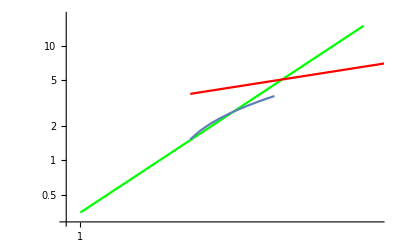

```mathematica
Show[LogLogPlot[{.35 x^8},{x,1,1.6},PlotStyle->{Green}],ListLogLogPlot[TabαSol[[1;;10,{1,2}]],Joined->True],LogLogPlot[{2.7 x^1.9},{x,1.2,28},PlotStyle->{Red}]]
```

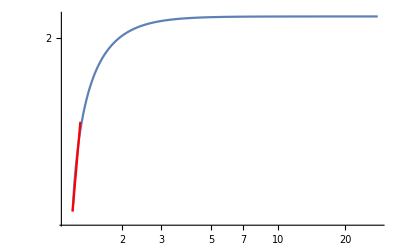

```mathematica
Show[ListLogLogPlot[TabαSol[[1;;,{1,3}]],Joined->True,PlotRange->Full],LogLogPlot[0.52 x^4,{x,1.2,1.3},PlotStyle->Red]]
```

```mathematica
Export["tau_xmax_vs_rhormax.dat",TabαSol,"Data"]
```

tau_xmax_vs_rhormax.dat

```mathematica
LogLogPlot[{1/X 1/(2 (1+X) (1+τ^2)^2)τ^2 (-2 X (1+τ^2)+4 (1+X) τ ArcTan[X/τ]+2 (1+X) (-1+τ^2) Log[(1+X) τ]-(1+X) (-1+τ^2) Log[X^2+τ^2])/.X-> r/rs/.Solh},{r,0.01,100},Frame->True, FrameLabel->{"r [kpc]","(v^2)_max "},Epilog->{Directive[lineStyle],line1}]
```

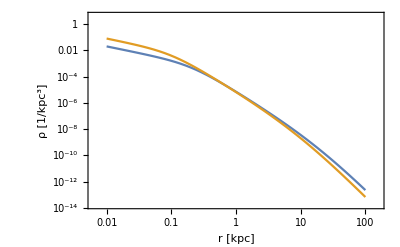

```mathematica
LogLogPlot[{1/(4π rs^3)1/(x(1+x)^2)(τ^2/(τ^2+x^2))/.x-> r/rs/.τ-> 0.01/.rs-> 20,1/(4π rs^3)1/(x(1+x)^2)(τ^2/(τ^2+x^2))/.x-> r/rs/.τ-> 0.01/.rs-> 10},{r,0.01,100},Frame->True, FrameLabel->{"r [kpc]","ρ [1/kpc^3]"}]
```

## Instead of finding actual solution, find closest tNFW halos that fit

```mathematica
Solclose2[rh_,rmax_]:=NMinimize[{((1/(1+Y) (-2 Y (1+τ^2)+4 (1+Y) τ ArcTan[Y/τ]+2 (1+Y) (-1+τ^2) Log[(1+Y) τ]-(1+Y) (-1+τ^2) Log[Y^2+τ^2])-(-1+(π-τ) τ+(-1+τ^2) Log[τ]))^2 + ((τ^2 (2 X (1+τ^2) (X+X^2+X^3+τ^2+2 X τ^2)-(1+X)^2 (X^2+τ^2) (4 τ ArcTan[X/τ]+(-1+τ^2) (2 Log[(1+X) τ]-Log[X^2+τ^2]))))/(2 X^2 (1+X)^2 (1+τ^2)^2 (X^2+τ^2)))^2)/. Y-> rh/rs /.X-> rmax/rs,τ>0, rs>rmax/2.16258},{τ,rs}, MaxIterations->1000,AccuracyGoal->8]
```

{2.66538×10^-6,{τ→0.898206,rs→1.52931}}

x_max= 0.806898

M_(1/2) = 0.499888

dv_max^2/dr(r_max) = -0.00161607

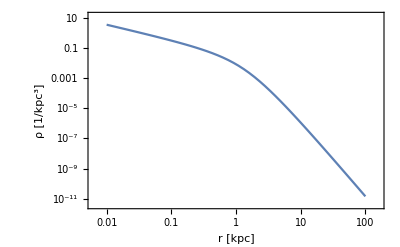

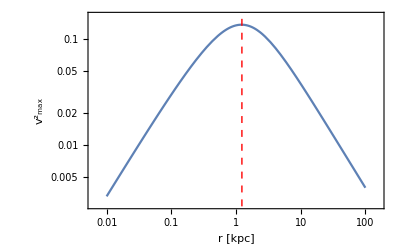

```mathematica
rmax =1.234;
α=1.16;
rh=α*rmax;
 Solh2 = Solclose2[rh,rmax]
Print["x_max= ", rmax/rs/. Solh2[[2]]]
Print["M_(1/2) = ",(1/(2(1+Y)) (-2 Y (1+τ^2)+4 (1+Y) τ ArcTan[Y/τ]+2 (1+Y) (-1+τ^2) Log[(1+Y) τ]-(1+Y) (-1+τ^2) Log[Y^2+τ^2])/. Y-> rh/rs)/(-1+(π-τ) τ+(-1+τ^2) Log[τ])/.Y-> rh/rs/.Solh2[[2]]]

Print["dv_max^2/dr(r_max) = ",(((τ^2 (2 X (1+τ^2) (X+X^2+X^3+τ^2+2 X τ^2)-(1+X)^2 (X^2+τ^2) (4 τ ArcTan[X/τ]+(-1+τ^2) (2 Log[(1+X) τ]-Log[X^2+τ^2]))))/(2 X^2 (1+X)^2 (1+τ^2)^2 (X^2+τ^2)))/.X-> rmax/rs)/.Solh2[[2]]]
LogLogPlot[{1/(4π rs^3)1/(x(1+x)^2)(τ^2/(τ^2+x^2))/.x-> r/rs/.Solh2[[2]]},{r,0.01,100},Frame->True, FrameLabel->{"r [kpc]","ρ [1/kpc^3]"}]
lineStyle={Thick,Red,Dashed};
line1=Line[{{Log[rmax],Log[10^-10]},{Log[rmax],Log[3000]}}];
LogLogPlot[{1/X 1/(2 (1+X) (1+τ^2)^2)τ^2 (-2 X (1+τ^2)+4 (1+X) τ ArcTan[X/τ]+2 (1+X) (-1+τ^2) Log[(1+X) τ]-(1+X) (-1+τ^2) Log[X^2+τ^2])/.X-> r/rs/.Solh2[[2]]},{r,0.01,100},Frame->True, FrameLabel->{"r [kpc]","(v^2)_max "},Epilog->{Directive[lineStyle],line1}]
```

### Tabulate approximate solution

```mathematica
rmax=1.234;
TabαSolapprox = ParallelTable[SolT =Solclose2[α rmax,rmax][[2]];{α,SolT[[1,2]],rmax/SolT[[2,2]]},{α,0.55,1.17,0.005}];
```

```mathematica
rmax=1.234;
TabαSolapprox2 = ParallelTable[SolT =Solclose2[α rmax,rmax][[2]];{α,SolT[[1,2]],rmax/SolT[[2,2]]},{α,1.16,1.18,0.001}];
```

```mathematica
TabαSolapprox
```

{{0.55,1.3268,2.16258},{0.555,1.34656,2.16258},{0.56,1.36642,2.16258},{0.565,1.3864,2.16258},{0.57,1.40649,2.16258},{0.575,1.42669,2.16258},{0.58,1.447,2.16258},{0.585,1.46742,2.16258},{0.59,1.48796,2.16258},{0.595,1.5086,2.16258},{0.6,1.52935,2.16258},{0.605,1.55021,2.16258},{0.61,1.57119,2.16258},{0.615,1.59227,2.16258},{0.62,1.61346,2.16258},{0.625,1.63476,2.16258},{0.63,1.65617,2.16258},{0.635,1.67769,2.16258},{0.64,1.69932,2.16258},{0.645,1.72105,2.16258},{0.65,1.7429,2.16258},{0.655,1.76485,2.16258},{0.66,1.78691,2.16258},{0.665,1.80909,2.16258},{0.67,1.83136,2.16258},{0.675,1.85375,2.16258},{0.68,1.87624,2.16258},{0.685,1.89884,2.16258},{0.69,1.92155,2.16258},{0.695,1.94437,2.16258},{0.7,1.96729,2.16258},{0.705,1.99032,2.16258},{0.71,2.01346,2.16258},{0.715,2.0367,2.16258},{0.72,2.06006,2.16258},{0.725,2.08351,2.16258},{0.73,2.10708,2.16258},{0.735,2.13075,2.16258},{0.74,2.15453,2.16258},{0.745,2.17841,2.16258},{0.75,2.2024,2.16258},{0.755,2.22649,2.16258},{0.76,2.2507,2.16258},{0.765,2.275,2.16258},{0.77,2.29941,2.16258},{0.775,2.32393,2.16258},{0.78,2.34855,2.16258},{0.785,2.37328,2.16258},{0.79,2.39811,2.16258},{0.795,2.42305,2.16258},{0.8,2.44809,2.16258},{0.805,2.47323,2.16258},{0.81,2.49848,2.16258},{0.815,2.52384,2.16258},{0.82,2.5493,2.16258},{0.825,2.57486,2.16258},{0.83,2.60053,2.16258},{0.835,2.6263,2.16258},{0.84,2.65217,2.16258},{0.845,2.67815,2.16258},{0.85,2.70423,2.16258},{0.855,2.73041,2.16258},{0.86,2.7567,2.16258},{0.865,2.78309,2.16258},{0.87,2.80958,2.16258},{0.875,2.83617,2.16258},{0.88,2.86287,2.16258},{0.885,2.88967,2.16258},{0.89,2.91657,2.16258},{0.895,2.94358,2.16258},{0.9,2.97068,2.16258},{0.905,2.99789,2.16258},{0.91,3.0252,2.16258},{0.915,3.05262,2.16258},{0.92,3.08013,2.16258},{0.925,3.10774,2.16258},{0.93,3.13546,2.16258},{0.935,3.16328,2.16258},{0.94,3.1912,2.16258},{0.945,3.21922,2.16258},{0.95,3.24734,2.16258},{0.955,3.27557,2.16258},{0.96,3.30389,2.16258},{0.965,3.33231,2.16258},{0.97,3.36084,2.16258},{0.975,3.38947,2.16258},{0.98,3.41819,2.16258},{0.985,3.44702,2.16258},{0.99,3.47594,2.16258},{0.995,3.50497,2.16258},{1.,3.5341,2.16258},{1.005,2.35339,1.68053},{1.01,1.94971,1.49056},{1.015,1.78006,1.40279},{1.02,1.66294,1.33887},{1.025,1.57176,1.28702},{1.03,1.49916,1.24411},{1.035,1.43736,1.20649},{1.04,1.38429,1.17325},{1.045,1.33788,1.14341},{1.05,1.29684,1.11638},{1.055,1.26015,1.09165},{1.06,1.22709,1.06888},{1.065,1.1971,1.0478},{1.07,1.16969,1.02816},{1.075,1.1446,1.00982},{1.08,1.12145,0.992606},{1.085,1.10002,0.976394},{1.09,1.08012,0.961084},{1.095,1.06157,0.946581},{1.1,1.04424,0.932814},{1.105,1.028,0.919713},{1.11,1.01273,0.907221},{1.115,0.998357,0.895285},{1.12,0.984739,0.883836},{1.125,0.971953,0.872911},{1.13,0.959791,0.862397},{1.135,0.948246,0.852287},{1.14,0.937268,0.842553},{1.145,0.926813,0.833169},{1.15,0.916895,0.824143},{1.155,0.907434,0.815427},{1.16,0.898185,0.806886},{1.165,0.889482,0.798703},{1.17,0.881118,0.790762}}

```mathematica
TabαSolapprox2
```

{{1.16,0.898206,0.806898},{1.161,0.89811,0.806164},{1.162,0.894715,0.803612},{1.163,0.892927,0.80195},{1.164,0.893337,0.801502},{1.165,0.889483,0.798703},{1.166,0.887877,0.797148},{1.167,0.890529,0.797942},{1.168,0.886555,0.795085},{1.169,0.886506,0.794393},{1.17,0.889904,0.795595},{1.171,0.879631,0.789283},{1.172,0.891949,0.795386},{1.173,0.888149,0.792643},{1.174,0.874669,0.784582},{1.175,0.941676,0.820248},{1.176,1.00127,0.851002},{1.177,1.04297,0.871839},{1.178,1.07798,0.88893},{1.179,1.10863,0.903588},{1.18,1.13602,0.916446}}

```mathematica
Export["tau_xmax_vs_rhormax_low.dat",TabαSolapprox,"Data"]
```

tau_xmax_vs_rhormax_low.dat

```mathematica
Export["tau_xmax_vs_rhormax_mid.dat",TabαSolapprox2 ,"Data"]
```

tau_xmax_vs_rhormax_mid.dat

## Change the truncation behavior to a steeper one

### Compute half-mass

```mathematica
mhalf=FullSimplify[Assuming[{τ,Y} ∈Reals && τ >0&&Y>0,Integrate[x/(1+x)^2(τ^2/(τ^2+x^2))^2,{x,0,Y}]]];
```

### Compute total mass

```mathematica
mtot = FullSimplify[Assuming[τ ∈Reals && τ >0,Integrate[x/(1+x)^2(τ^2/(τ^2+x^2))^2,{x,0,Infinity}]]];
```

### Plot the 2 cases for an examples

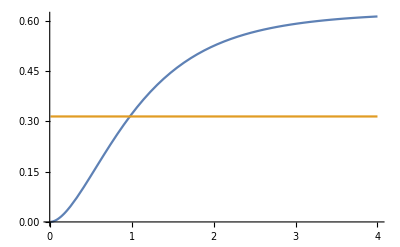

```mathematica
Plot[{2*mhalf/.τ-> 2,mtot/.τ-> 2},{Y,.01,4},PlotRange->Full]
```

#### Solve for the solution

```mathematica
tauSol[Y_]:=FindRoot[2 mhalf==mtot,{τ,3 Y^1.2}]
```

### Make a table of solutions

```mathematica
τTab = Table[{Y,tauSol[Y][[1,2]]},{Y,0.001,2,0.001}];
```

### Plot it

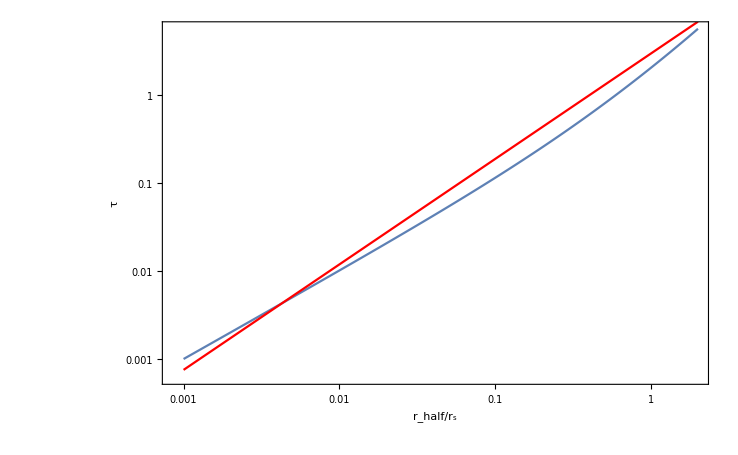

```mathematica
Show[ListLogLogPlot[τTab,Joined-> True,Frame->True,FrameLabel-> {Subscript[r, half]/Subscript[r, s],τ},LabelStyle->Directive[Bold, Medium,25],PlotRange->Full],LogLogPlot[3 x^1.2,{x,0.001,2},PlotStyle->Red]]
```

#### Now handle vmax

```mathematica
FullSimplify[Assuming[{Y,τ} ∈Reals && Y>0 && τ>0,Difvmax = D[1/Y mhalf,Y]]];
```

```mathematica
Tabtau[τh_]:= FindRoot[Difvmax/.τ-> τh,{Y,0.9τh}]
```

### Make a table of solutions

```mathematica
XmaxTab = Table[{τ,Tabtau[τ][[1,2]]},{τ,.001,1,0.001}];
```

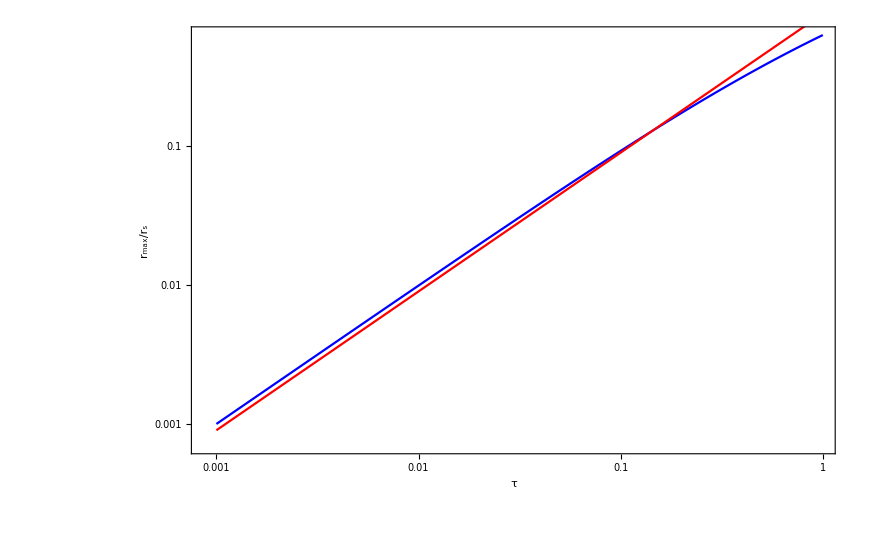

```mathematica
Show[ListLogLogPlot[{XmaxTab},Joined-> True,Frame->True,PlotRange->Full,FrameLabel-> {τ,Subscript[r, max]/Subscript[r, s]},LabelStyle->Directive[Bold, Medium,25],PlotStyle->{Blue,Red}],LogLogPlot[0.9x,{x,0.001,1},PlotStyle->Red]]
```

```mathematica
tautab = Table[{XmaxTab[[i,2]],XmaxTab[[i,1]]},{i,2,Length[XmaxTab]}];
```

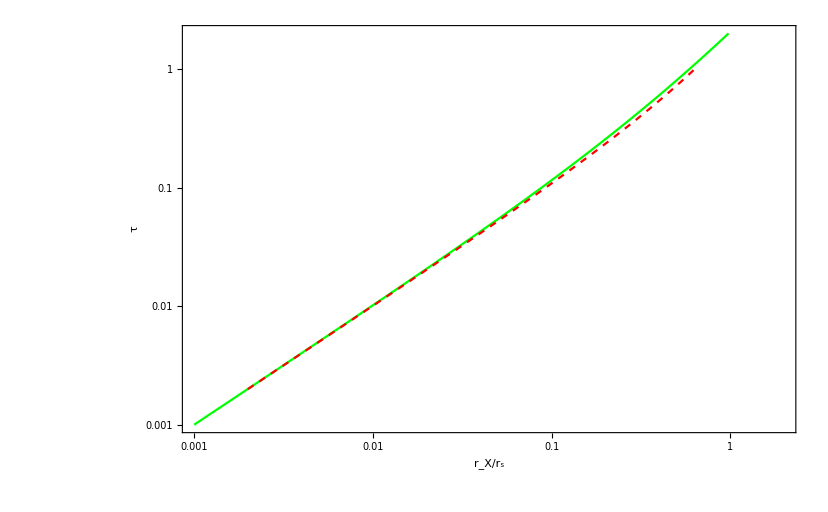

```mathematica
ListLogLogPlot[{τTab,tautab },PlotRange->{{0.001,2},{0.001,2}},Joined-> True,Frame->True,FrameLabel-> {Subscript[r, X]/Subscript[r, s],τ},LabelStyle->Directive[Bold, Medium,25],PlotStyle->{Green,{Red,Dashed}}]
```

## Try a pseudo-jaffe profile

FindRoot[{(-1+1/(1+Y)+ArcTan[Y]/.Y→1.31683/rt)==1/4 (-2+π),(((X (1+X (3+X+X^2)))/((1+X)^2 (1+X^2))-ArcTan[X])/(2 X^2)/.X→1.1352/rt)==0},{{rt,1.1352,0,150 1.1352}},MaxIterations→1000,AccuracyGoal→8]

x_max= 1.1352/rt/.FindRoot[{(-1+1/(1+Y)+ArcTan[Y]/.Y→1.31683/rt)==1/4 (-2+π),(((X (1+X (3+X+X^2)))/((1+X)^2 (1+X^2))-ArcTan[X])/(2 X^2)/.X→1.1352/rt)==0},{{rt,1.1352,0,150 1.1352}},MaxIterations→1000,AccuracyGoal→8]

M_(1/2) = (4 (-1+1/(1+1.31683/rt)+ArcTan[1.31683/rt]))/(-2+π)/.FindRoot[{(-1+1/(1+Y)+ArcTan[Y]/.Y→1.31683/rt)==1/4 (-2+π),(((X (1+X (3+X+X^2)))/((1+X)^2 (1+X^2))-ArcTan[X])/(2 X^2)/.X→1.1352/rt)==0},{{rt,1.1352,0,150 1.1352}},MaxIterations→1000,AccuracyGoal→8]

dv_max^2/dr(r_max) = 0.387994 rt^2 ((1.1352 (1+(1.1352 (3+1.28868/rt^2+1.1352/rt))/rt))/((1+1.28868/rt^2) (1+1.1352/rt)^2 rt)-ArcTan[1.1352/rt])/.FindRoot[{(-1+1/(1+Y)+ArcTan[Y]/.Y→1.31683/rt)==1/4 (-2+π),(((X (1+X (3+X+X^2)))/((1+X)^2 (1+X^2))-ArcTan[X])/(2 X^2)/.X→1.1352/rt)==0},{{rt,1.1352,0,150 1.1352}},MaxIterations→1000,AccuracyGoal→8]

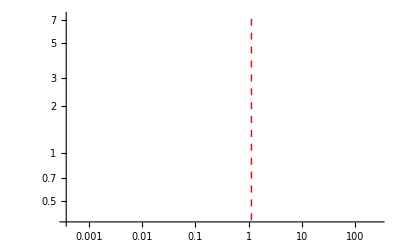

```mathematica
rmax =1.1352;
α=1.16;
rh=α*rmax;
Solh2 = Solrt[rh,rmax,rmax]
Print["x_max= ", rmax/rt /. Solh2]
Print["M_(1/2) = ",(-1+1/(1+Y)+ArcTan[Y])/(1/4 (-2+π))/.Y-> rh/rt/.Solh2]

Print["dv_max^2/dr(r_max) = ",((X (1+X (3+X+X^2)))/((1+X)^2 (1+X^2))-ArcTan[X])/(2 X^2)/.X-> rmax/rt/.Solh2]
lineStyle={Thick,Red,Dashed};
line1=Line[{{Log[rmax],Log[10^-10]},{Log[rmax],Log[3000]}}];
LogLogPlot[1/X 1/2 (-1+1/(1+X)+ArcTan[X])/.X-> r/rt/. Solh2,{r,0.001,100},Epilog->{Directive[lineStyle],line1}]
```

## Now for the Burkert profile

### Compute half-mass

```mathematica
mhalf=FullSimplify[Assuming[{τ,X} ∈Reals && τ >1&&X>0,Integrate[x^2/((1+x)(1+x^2))(τ^2/(τ^2+x^2)),{x,0,X}]]]
```

(τ^2 (-2 (1+τ^2) ArcTan[X]+4 τ ArcTan[X/τ]-2 Log[1+X]+(1+τ^2) Log[1+X^2]+2 τ^2 Log[((1+X) τ^2)/(X^2+τ^2)]))/(4 (-1+τ^4))

### Compute total mass

```mathematica
mtot=FullSimplify[Assuming[{τ,X} ∈Reals && τ >1&&X>0,Integrate[x^2/((1+x)(1+x^2))(τ^2/(τ^2+x^2)),{x,0,Infinity}]]]
```

(τ^2 (-π (-1+τ)^2+4 τ^2 Log[τ]))/(4 (-1+τ^4))

### Plot the 2 cases for an examples

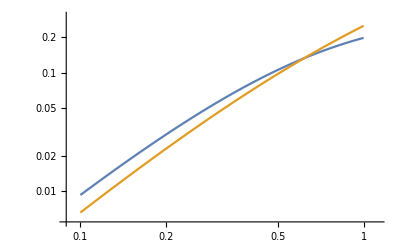

```mathematica
LogLogPlot[{2*mhalf/.X->1.1,mtot},{τ,0.1,1}]
```

### Ok they intersect, find solution numerically

```mathematica
tauSolB[Xh_]:=FindRoot[(2mhalf/.X-> Xh)==mtot,{τ,0.5 Xh^2}]
```

### Make a table of solutions

```mathematica
τTabB = Table[{X,tauSolB[X][[1,2]]},{X,0.55,45,0.05}];
```

#### Plot it

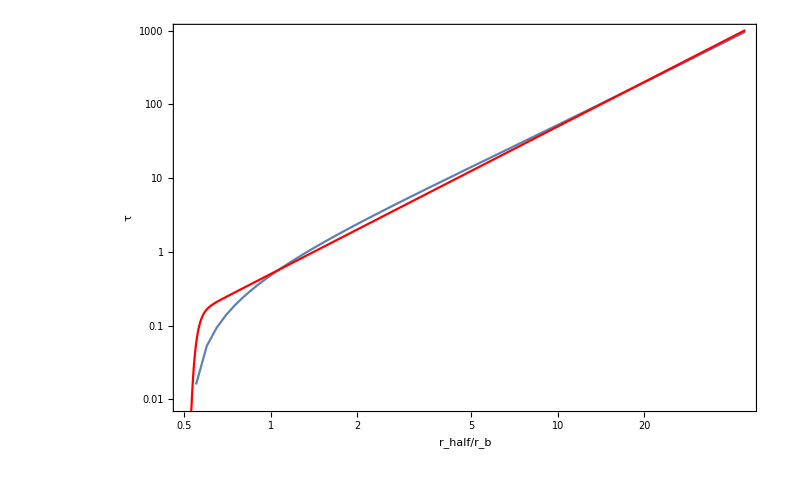

```mathematica
Show[ListLogLogPlot[τTabB,Joined-> True,Frame->True,FrameLabel-> {Subscript[r, half]/Subscript[r, b],τ},LabelStyle->Directive[Bold, Medium,25],PlotRange->Full],LogLogPlot[0.5 x^2 Exp[-(0.55/x)^29],{x,0.01,45},PlotStyle->Red]]
```

```mathematica
Export["tau_vs_rhalf0rburk.dat",τTabB,"Data"]
```

tau_vs_rhalf0rburk.dat

#### Do the vmax constraints

```mathematica
FullSimplify[Assuming[{X,τ} ∈Reals && X>0 && τ>0,Difvmax = D[1/X mhalf,X]]];
```

```mathematica
TabtauB[τh_]:= FindRoot[Difvmax/.τ-> τh,{X,1.3 τh^0.3}]
```

### Find maximum value of xmax

```mathematica
Series[Difvmax,{τ,Infinity,2}]
```

(X/((1+X) (1+X^2))+ArcTan[X]/(2 X^2)-Log[1+X]/(2 X^2)-Log[1+X^2]/(4 X^2))+(1/2-1/X-X^3/((1+X) (1+X^2))+ArcTan[X]/(2 X^2)+Log[1+X]/(2 X^2)-Log[1+X^2]/(4 X^2))/τ^2+O[1/τ]^3

```mathematica
FindRoot[(X/((1+X) (1+X^2))+ArcTan[X]/(2 X^2)-Log[1+X]/(2 X^2)-Log[1+X^2]/(4 X^2)) ==0,{X,3}]
```

{X→3.24463}

### Make a table of solutions

```mathematica
XmaxTabB = Table[{τ,TabtauB[τ][[1,2]]},{τ,.01,100,0.05}];
```

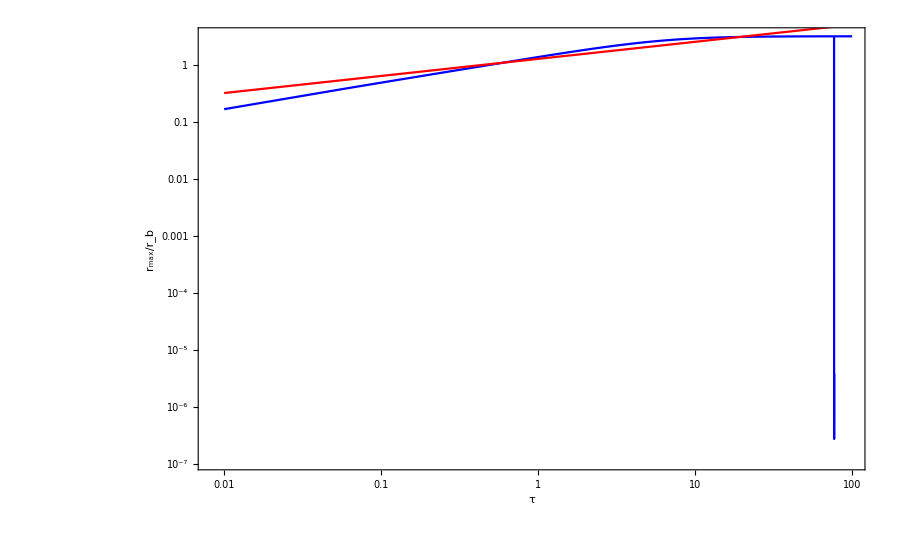

```mathematica
Show[ListLogLogPlot[{XmaxTabB},Joined-> True,Frame->True,PlotRange->Full,FrameLabel-> {τ,Subscript[r, max]/Subscript[r, b]},LabelStyle->Directive[Bold, Medium,25],PlotStyle->{Blue}],LogLogPlot[1.3 x^0.3,{x,0.01,100},PlotStyle->Red]]
```

```mathematica
tautabB = Table[{XmaxTabB[[i,2]],XmaxTabB[[i,1]]},{i,2,Length[XmaxTabB]}];
```

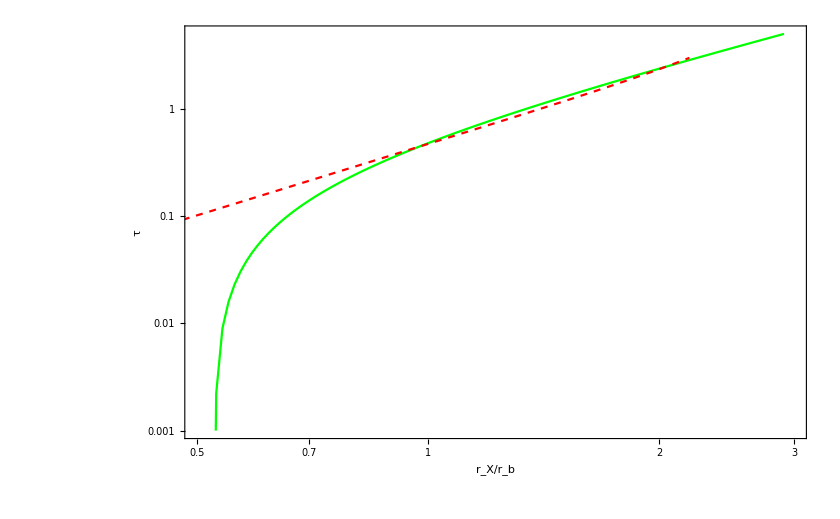

```mathematica
ListLogLogPlot[{τTabB,tautabB },PlotRange->{{0.5,3},{0.001,5}},Joined-> True,Frame->True,FrameLabel-> {Subscript[r, X]/Subscript[r, b],τ},LabelStyle->Directive[Bold, Medium,25],PlotStyle->{Green,{Red,Dashed}}]
```

```mathematica
SolBurk[rh_,rmax_,τs_,rbs_]:=FindRoot[{(2mhalf/. X-> rh/rb)/mtot==1,(Difvmax/.X-> rmax/rb)==0},{{τ,τs,0,3000},{rb,rbs,rmax/3.24462,15*rmax}}, MaxIterations->1000,AccuracyGoal->8]
```

{τ→3.32428,rb→0.499484}

x_max= 2.27275

M_(1/2) = 0.5

dv_max^2/dr(r_max) = 0.

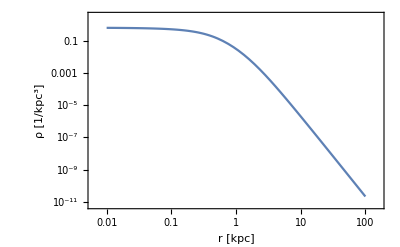

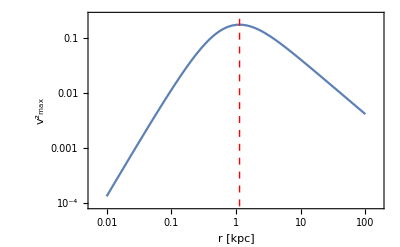

```mathematica
rmax =1.1352;
α=1.04;
rh=α*rmax;
Solh=SolBurk[rh,rmax,5.26 α^2,rmax/2.3]
Print["x_max= ", rmax/rb/. Solh]
Print["M_(1/2) = ",(mhalf/. X-> rh/rb)/mtot/.Solh]

Print["dv_max^2/dr(r_max) = ",Difvmax/.X-> rmax/rb/.Solh]
LogLogPlot[{1/(4π rb^3)1/((1+x)(1+x^2))(τ^2/(τ^2+x^2))/.x-> r/rb/.Solh},{r,0.01,100},Frame->True, FrameLabel->{"r [kpc]","ρ [1/kpc^3]"}]
lineStyle={Thick,Red,Dashed};
line1=Line[{{Log[rmax],Log[10^-10]},{Log[rmax],Log[3000]}}];
LogLogPlot[{1/X mhalf/.X-> r/rb/.Solh},{r,0.01,100},Frame->True, FrameLabel->{"r [kpc]","(v^2)_max "},Epilog->{Directive[lineStyle],line1}]
```

### Tabulate solutions

```mathematica
rmax=1.234;
TabSol = ParallelTable[SolT = SolBurk[α rmax,rmax,5.26 α^2,rmax/2];{α,SolT[[1,2]],rmax/SolT[[2,2]]},{α,0.96,14,0.01}];
```

Power::infy: Infinite expression 1/0. encountered.

Power::infy: Infinite expression 1/0.^2 encountered.

FindRoot::nlnum: The function value {Indeterminate, Indeterminate} is not a list of numbers with dimensions {2} at {τ, rb} = {0., 1.67633}.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power :: infy will be suppressed during this calculation.

FindRoot::nlnum: The function value {Indeterminate, Indeterminate} is not a list of numbers with dimensions {2} at {τ, rb} = {0., 0.961979}.

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

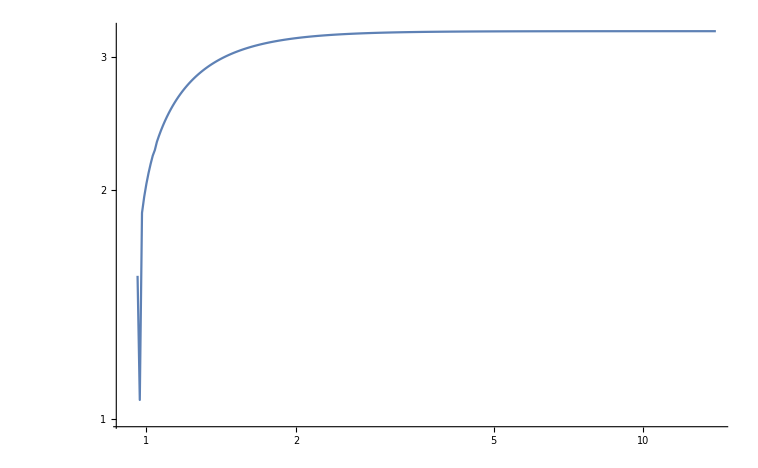

```mathematica
ListLogLogPlot[TabSol[[1;;,{1,3}]],PlotRange->Full,Joined->True]
```

```mathematica
Export["Burkert_fit.dat",TabSol,"Data"]
```

Burkert_fit.dat

```mathematica
0.66651 3.2446257246042656
```

2.16258